```mathematica
With[{α=1},NSolve[(t^2-(1-α))^2-α^2 t==0,t]]
```

{{t→-0.5-0.866025 ⅈ},{t→-0.5+0.866025 ⅈ},{t→0.},{t→1.}}

```mathematica
Solve[(t^2-(1-α))^2-α^2 t==0,t]
```

{{t→1},{t→-1/3-(2^(1/3) (-4+6 α))/(3 (16-36 α+27 α^2+3 √3 √(16 α^2-40 α^3+27 α^4))^(1/3))+((16-36 α+27 α^2+3 √3 √(16 α^2-40 α^3+27 α^4))^(1/3))/(3 2^(1/3))},{t→-1/3+((1+ⅈ √3) (-4+6 α))/(3 2^(2/3) (16-36 α+27 α^2+3 √3 √(16 α^2-40 α^3+27 α^4))^(1/3))-((1-ⅈ √3) (16-36 α+27 α^2+3 √3 √(16 α^2-40 α^3+27 α^4))^(1/3))/(6 2^(1/3))},{t→-1/3+((1-ⅈ √3) (-4+6 α))/(3 2^(2/3) (16-36 α+27 α^2+3 √3 √(16 α^2-40 α^3+27 α^4))^(1/3))-((1+ⅈ √3) (16-36 α+27 α^2+3 √3 √(16 α^2-40 α^3+27 α^4))^(1/3))/(6 2^(1/3))}}

```mathematica
With[{α=0},Solve[t==-1/3+((1+ⅈ √3) (-4+6 α))/(3 2^(2/3) (16-36 α+27 α^2+3 √3 √(16 α^2-40 α^3+27 α^4))^(1/3))-((1-ⅈ √3) (16-36 α+27 α^2+3 √3 √(16 α^2-40 α^3+27 α^4))^(1/3))/(6 2^(1/3))]]
```

{{t→-1}}

```mathematica
With[{α=1},Solve[t==-1/3+((1+ⅈ √3) (-4+6 α))/(3 2^(2/3) (16-36 α+27 α^2+3 √3 √(16 α^2-40 α^3+27 α^4))^(1/3))-((1-ⅈ √3) (16-36 α+27 α^2+3 √3 √(16 α^2-40 α^3+27 α^4))^(1/3))/(6 2^(1/3))]]
```

{{t→1/2 (-1+ⅈ √3)}}

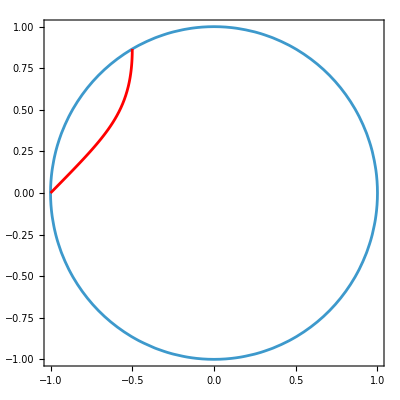

```mathematica
Show[
	 ContourPlot[
	   x^2+y^2==1,
	   {x,-1,1},
	   {y,-1,1},
	   PlotRange->{{-1,1},{-1,1}}
	 ],
	 ParametricPlot[
	 {
	   Re[-1/3+((1+ⅈ √3) (-4+6 α))/(3 2^(2/3) (16-36 α+27 α^2+3 √3 √(16 α^2-40 α^3+27 α^4))^(1/3))-((1-ⅈ √3) (16-36 α+27 α^2+3 √3 √(16 α^2-40 α^3+27 α^4))^(1/3))/(6 2^(1/3))],
	   Im[-1/3+((1+ⅈ √3) (-4+6 α))/(3 2^(2/3) (16-36 α+27 α^2+3 √3 √(16 α^2-40 α^3+27 α^4))^(1/3))-((1-ⅈ √3) (16-36 α+27 α^2+3 √3 √(16 α^2-40 α^3+27 α^4))^(1/3))/(6 2^(1/3))]},
	 {α,0,1},
	   PlotRange->{{-1,1},{-1,1}},
	   AxesLabel->{"Re","Im"},
	   PlotStyle->Red
	 ]
]
```

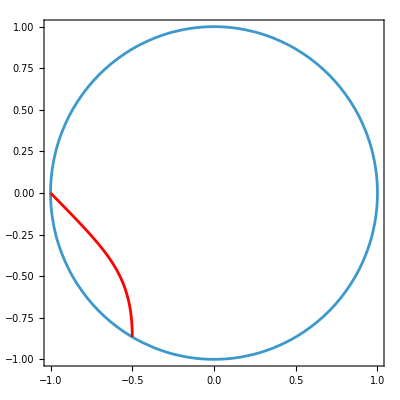

```mathematica
Show[
	 ContourPlot[
	   x^2+y^2==1,
	   {x,-1,1},
	   {y,-1,1},
	   PlotRange->{{-1,1},{-1,1}}
	 ],
	 ParametricPlot[
	 {
	   Re[-1/3+((1-ⅈ √3) (-4+6 α))/(3 2^(2/3) (16-36 α+27 α^2+3 √3 √(16 α^2-40 α^3+27 α^4))^(1/3))-((1+ⅈ √3) (16-36 α+27 α^2+3 √3 √(16 α^2-40 α^3+27 α^4))^(1/3))/(6 2^(1/3))],
	   Im[-1/3+((1-ⅈ √3) (-4+6 α))/(3 2^(2/3) (16-36 α+27 α^2+3 √3 √(16 α^2-40 α^3+27 α^4))^(1/3))-((1+ⅈ √3) (16-36 α+27 α^2+3 √3 √(16 α^2-40 α^3+27 α^4))^(1/3))/(6 2^(1/3))]},
	 {α,0,1},
	   PlotRange->{{-1,1},{-1,1}},
	   AxesLabel->{"Re","Im"},
	   PlotStyle->Red
	 ]
]
```